```mathematica
Integrate[Exp[-I*xi*r*Cos[t]],{t,0,2Pi}]
```

ConditionalExpression[2 π BesselJ[0,r xi], r xi∈ℝ]

```mathematica
Integrate[BesselJ[0,r*xi],{xi,0,Infinity}]
```

ConditionalExpression[Piecewise[{{-1/r, Re[r]<0&&Im[r]==0}, {1/r, True}}], r∈ℝ]

```mathematica
Solve[x^5-1==0,x]
```

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

```mathematica
N[{{x->1},{x->-(-1)^(1/5)},{x->(-1)^(2/5)},{x->-(-1)^(3/5)},{x->(-1)^(4/5)}}]
```

{{x→1.},{x→-0.809017-0.587785 ⅈ},{x→0.309017+0.951057 ⅈ},{x→0.309017-0.951057 ⅈ},{x→-0.809017+0.587785 ⅈ}}

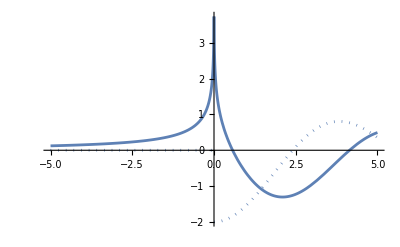

```mathematica
ReImPlot[StruveH[0,-x]-BesselY[0,-x],{x,-5,5}]
```

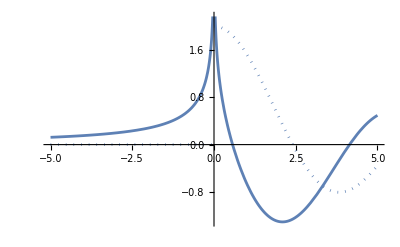

```mathematica
ReImPlot[-StruveH[0,x]-BesselY[0,x]+2I BesselJ[0,x],{x,-5,5}]
```

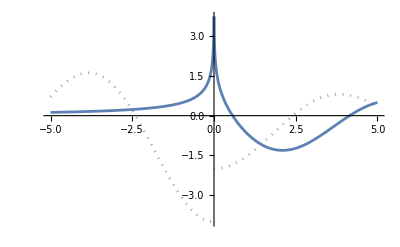

```mathematica
ReImPlot[-StruveH[0,x]-BesselY[0,x]-2I BesselJ[0,x],{x,-5,5}]
```

```mathematica
x = 3 + 2I;
N[StruveH[0,x]-BesselY[0,x]];
N[BesselJ[0,x] + I*StruveH[0,x]]
```

0.0700183+0.19884 ⅈ

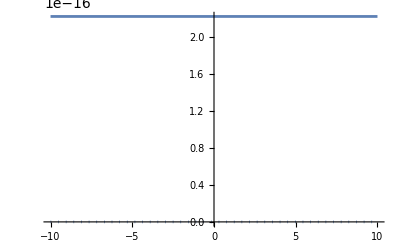

```mathematica
b = 2;
g = -1;
p0 =( y^5 -b y+g == 0);
rts = List @@ NRoots[p0,y][[All,2]];
pf = 1./ (5*rts^4-b);
ReImPlot[Sum[rts[[i]],{i,1,5}] ,{x, -10, 10}]
```

```mathematica
rts
```

{-1.,-0.51879,0.114071-1.21675 ⅈ,0.114071+1.21675 ⅈ,1.29065}

```mathematica
pf
```

{0.333333,-0.610571,0.0965103-0.0469031 ⅈ,0.0965103+0.0469031 ⅈ,0.0842175}